# Name:

Show an appropriate amount of work.  You can (and probably should) check your work with a computer.

Compute the magnitude and argument for

z=(ⅈ/(1+ⅈ))^3              
 abs(z)=                                           
 arg(z)=

z=((1+ⅈ)/(√(1+3ⅈ)))^3              
abs(z)=                                             
 arg(z)=

The roots of z^4=-64     
 abs(z)=                                            
 arg(z)=

The roots of z^2+2 ⅈ z+5=0     
 abs(z)=                                            
 arg(z)=

z=ⅈ^ⅈ  
 abs(z)=                                            
 arg(z)=

Compute the real and imaginary parts for

z=(ⅈ/(1+ⅈ))^3              
 z=                                           +ⅈ

z=((1+ⅈ)/(√(1+3ⅈ)))^3              
 z=                                           +ⅈ

The roots of z^3=-64     
 z_1=                                           +ⅈ                                            
 z_2=                                           +ⅈ                                            
z_3=                                           +ⅈ

The roots of z^2+2 ⅈ z+5=0     
 z_1=                                           +ⅈ                                            
 z_2=                                           +ⅈ

z=ⅈ^ⅈ   
 z=                                           +ⅈ

Sketch Points

Sketch the set of points C_1 that satisfy |z-2|<1. Make sure you label the set.

Sketch the set of points C_2 that satisfy im(z-2)=1. Make sure you label the set.

Sketch the set of points C_3 that satisfy arg(z-2)=π/4. Make sure you label the set.

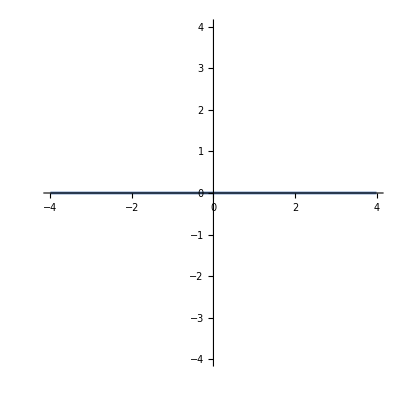

For f(z)=u(x,y)+ⅈ v(x,y) and write down the CR equations
                                             and

For cos(z) complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No

For ⅈ x^2-2 x y-ⅈ y^2 complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No                                              .  
If yes f(z)=

For ⅈ x^2-2 x y- y^2 complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No                                              .  
If yes f(z)=

Is ⅇ^(x-ⅈ y) analytic? Yes or No                                              .  Show your work below.

Label poles with P_1,P_2,… Label zeros with Z_1,Z_2,… 
Res(f,P_1)=                                             
Res(f,P_2)=

```mathematica
f[z_]:=3(z-1+ⅈ)/(1+z^2)
ComplexPlot3D[ f[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

Complete the following.  The TS arctan(z)=∑_(k=0)^∞ a_k z^k where a_k=                                                             converges for                                                              . Justify your convergence statement using a Calculus II theorem.   Give a simpler complex analytic justification below.

Complete the following.  The TS log(2+z)=∑_(k=0)^∞ a_k z^k where a_k=                                                             converges for                                                              . Justify your convergence statement using a Calculus II theorem.   Give a simpler complex analytic justification below.

Label and explain the singularity and color discontinuity visible in the plot below using appropriate language. The TS f(z)=∑_(k=0)^∞ (a_k(z-z_0))^k with z_0=-2+2ⅈ has 
a_k=                                                             and converges for |z-z_0|<                                                   . Explain what the TS converges to around the color discontinuity.

```mathematica
f[z_]:=Log[1+z]
ComplexPlot3D[ f[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

Label and explain the singularity and color discontinuity visible in the plots below using appropriate language. Explain why you might expect f_1to match f_2.  Explain why they do not match using appropriate language.

```mathematica
f1[z_]:=√(1-z^2)
f2[z_]:=ⅈ √(z^2-1)
{ComplexPlot3D[ f1[z],{z,2},PlotLabel->"f1"],ComplexPlot3D[ f2[z],{z,2},PlotLabel->"f2"]}
```

{-Graphics3D-,-Graphics3D-}

For the closed counter clockwise contour Γ shown below 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt.
For f(z)=z^2 evaluate ∫_Γ f(z)dz=                                                  and ∫_Γ_1 f(z)dz=                                                 .  Show appropriate work below.

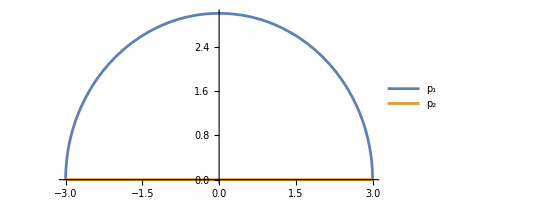

```mathematica
p1[t_]:=3 E^(π ⅈ t)
p2[t_]:=-3+6 t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]]},{t,0,1},PlotLegends->{"p_1","p_2"}]
```

For the closed counter clockwise contour Γ shown below 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
p_3(t)=                                                              for 0≤t<1 0≤t<1
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt+∫_0^1                                           dt
For f(z)=ⅈ/(z-(1+2ⅈ)) evaluate ∫_Γ f(z)dz=                                                  and ∫_Γ_3 f(z)dz=                                                 .  Show appropriate work below.

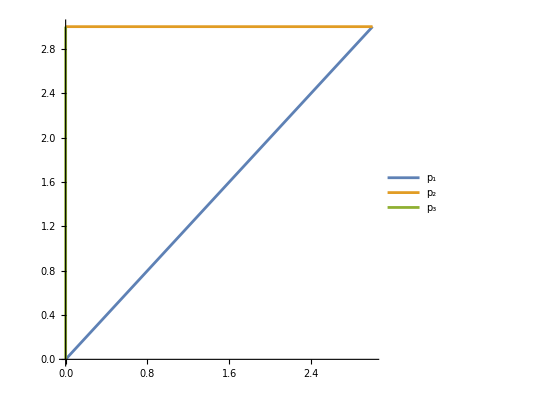

```mathematica
p1[t_]:=(3+3 ⅈ)t
p2[t_]:=3+3ⅈ -3 t
p3[t_]:= 3 ⅈ - 3 ⅈ t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]],ReIm[p3[t]]},{t,0,1},PlotLegends->{"p_1","p_2","p_3"}]
```

Compute ∫_Γ ⅇ^z/((z^2+4)(z-1))dz=                                                             for the counter clockwise contour Γ. Show appropriate work.

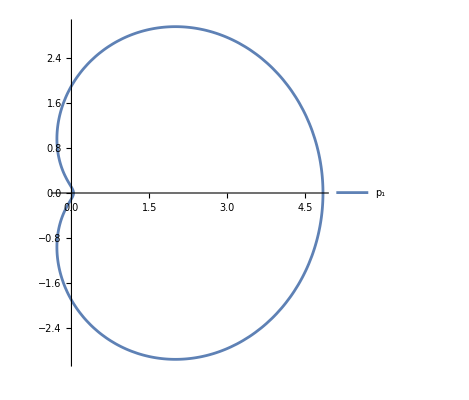

```mathematica
p1[t_]:=(E^(2π ⅈ t)+1.2)^2
ParametricPlot[ReIm[p1[t]],{t,0,1},PlotLegends->{"Γ"}]
```